### file imports & vectorisation

```mathematica
dataopen=Import["/home/filip/Desktop/c/archive/eurusd_analysis/output_open.txt","List"];
datahigh=Import["/home/filip/Desktop/c/archive/eurusd_analysis/output_high.txt","List"];
datalow=Import["/home/filip/Desktop/c/archive/eurusd_analysis/output_low.txt","List"];
dataclose=Import["/home/filip/Desktop/c/archive/eurusd_analysis/output_close.txt","List"];
```

```mathematica
vectorsopen=Table[{dataopen[[i]],dataopen[[i+1]]},{i,Length[dataopen]-1}];
vectorshigh=Table[{datahigh[[i]],datahigh[[i+1]]},{i,Length[datahigh]-1}];
vectorslow=Table[{datalow[[i]],datalow[[i+1]]},{i,Length[datalow]-1}];
vectorsclose=Table[{dataclose[[i]],dataclose[[i+1]]},{i,Length[dataclose]-1}];
```

### fázovy prostor a_(n+1)(a_n)

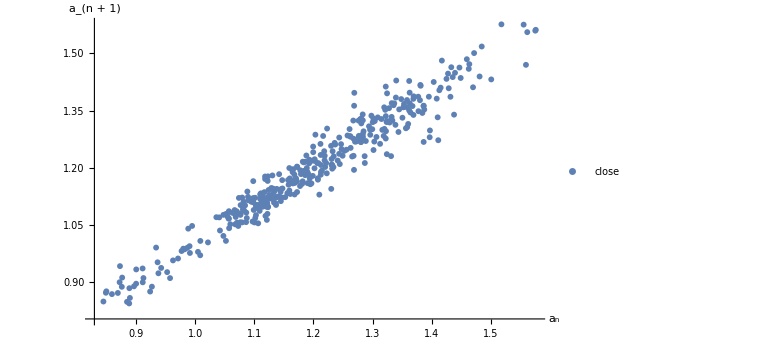
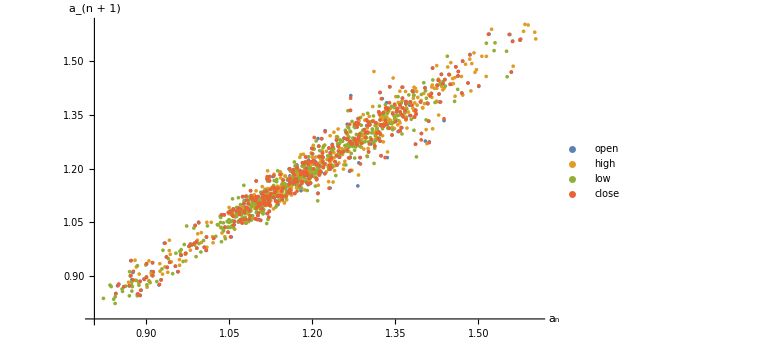

```mathematica
{ListPlot[vectorsclose,ImageSize->Large,PlotLegends->{"close"},AxesLabel->{"a_n","a_(n + 1)"}],ListPlot[{vectorsopen,vectorshigh,vectorslow,vectorsclose},ImageSize->Large,PlotLegends->{"open","high","low","close"},AxesLabel->{"a_n","a_(n + 1)"}]}
```

### delta histogram

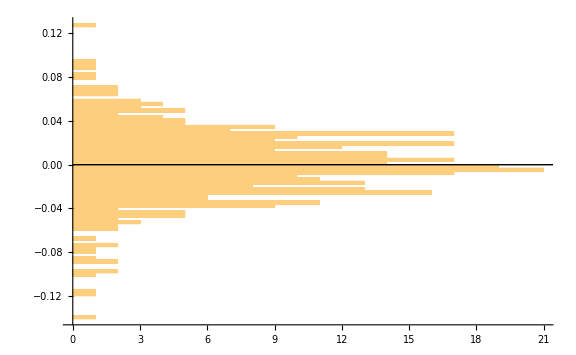

```mathematica
deltas=Table[dataclose[[i+1]]-dataclose[[i]],{i,Length[dataclose]-1}];
Histogram[deltas,{0.003},ImageSize->Large,BarOrigin->Left,Epilog->{ Line[{{0,0},{1000,0}}]}]
```

### distribution of delta mean size

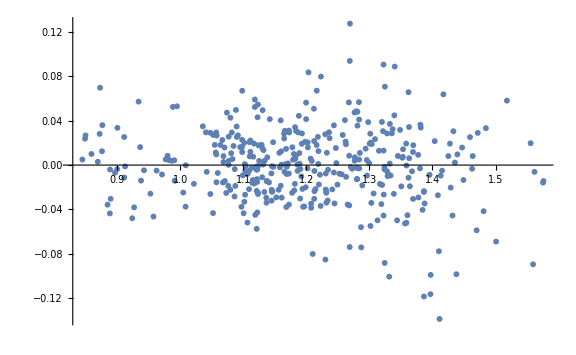

```mathematica
dms=Table[{dataclose[[i]],deltas[[i]]},{i,Length[dataclose]-1}];
ListPlot[dms,ImageSize->Large]
```

```mathematica
Manipulate[dms=Table[{dataclose[[i]],deltas[[i]]},{i,A}];
ListLinePlot[dms,ImageSize->Large,PlotRange->{-0.15,0.15},Epilog->{Red,PointSize[Large],Point[{dataclose[[A]],deltas[[A]]}]}],{A,1,Length[dataclose]-1,1}]
```

### fázový prostor a_(n+2)(a_(n+1),a_n)

```mathematica
trivectorsclose=Table[{dataclose[[i]],dataclose[[i+1]],dataclose[[i+2]]},{i,Length[dataclose]-2}];
ListPointPlot3D[trivectorsclose]
```

```mathematica
Manipulate[trivectorsclose=Table[{dataclose[[i]],dataclose[[i+1]],dataclose[[i+2]]},{i,A}];
ListLinePlot3D[trivectorsclose,ImageSize->Large],{A,1,Length[dataclose]-2,1}]
```